```mathematica
<<MaTeX`
```

```mathematica
path=NotebookDirectory[];
```

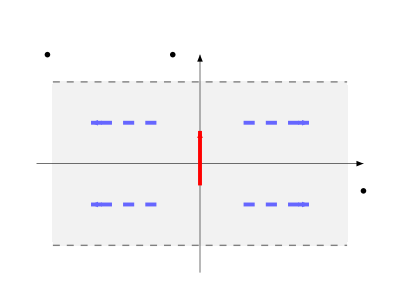

```mathematica
lines1=Graphics[{Red,Thickness[0.007],Arrowheads[0.05],
Arrow[{{0,-0.4},{0 ,0.6 }}]
}];

lines2=Graphics[{Black,Thickness[0.001],
Arrow[{{-3,0},{3 ,0 }}],
Arrow[{{0,-2},{0,2}}]
}];

lines3=Graphics[{Dashed,Gray,
Line[{{-2.7,1.5},{2.7 ,1.5 }}],
Line[{{-2.7,-1.5},{2.7 ,-1.5 }}]
}];

lines4a=Graphics[{Lighter[Blue,0.4],Dashing[0.02],Thickness[0.007],
Line[{{0.8,0.75},{1.9 ,0.75 }}],
Line[{{0.8,-0.75},{1.9 ,-0.75 }}],
Line[{{-0.8,0.75},{-1.9 ,0.75 }}],
Line[{{-0.8,-0.75},{-1.9 ,-0.75 }}]
}];
lines4b=Graphics[{Lighter[Blue,0.4],Thickness[0.007],Arrowheads[0.05],
Arrow[{{1.8,0.75},{2 ,0.75 }}],
Arrow[{{1.8,-0.75},{2 ,-0.75 }}],
Arrow[{{-1.8,0.75},{-2 ,0.75 }}],
Arrow[{{-1.8,-0.75},{-2 ,-0.75 }}]
}];

des=Graphics[{Black,Thin,
Text[Style[MaTeX["\\textbf{(b)} ",Magnification->1.6]],{-2.8,2}],
Text[Style[MaTeX["\\bm{z} ","Preamble"->{"\\usepackage{bm}"},Magnification->1.6]],{3,-0.5}],
Text[Style[MaTeX["\\bm{y} ","Preamble"->{"\\usepackage{bm}"},Magnification->1.6]],{-0.5,2}]
}];

p=Show[{lines2,lines1,lines3,lines4a,lines4b,des},BaseStyle->{
FontFamily->"Arial",
FontSize->14,
FontWeight->"Bold",Boxed->False
}];

a=Show[RegionPlot[Abs[y]<1.5&& Abs[x]<2.7,{x,-3,3},{y,-2,2.5},Frame-> False,Axes-> False,AxesStyle->Directive[Thickness[0.005],Gray],AspectRatio->4.5/6,PlotStyle->Directive[Lighter[Gray,0.9]],BoundaryStyle->None],p]
```

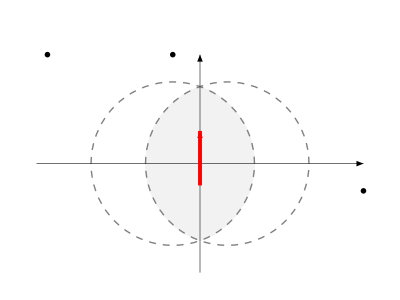

```mathematica
circle1=Graphics[{Dashed,Gray,Circle[{-0.5,0},1.5]}];
circle2=Graphics[{Dashed,Gray,Circle[{0.5,0},1.5]}];

lines1=Graphics[{Red,Thickness[0.007],Arrowheads[0.05],
Arrow[{{0,-0.4},{0 ,0.6 }}]
}];

lines2=Graphics[{Black,Thickness[0.001],
Arrow[{{-3,0},{3 ,0 }}],
Arrow[{{0,-2},{0,2}}]
}];

des=Graphics[{Black,Thin,
Text[Style[MaTeX["\\textbf{(a)} ",Magnification->1.6]],{-2.8,2}],
Text[Style[MaTeX["\\bm{x} ","Preamble"->{"\\usepackage{bm}"},Magnification->1.6]],{3,-0.5}],
Text[Style[MaTeX["\\bm{y} ","Preamble"->{"\\usepackage{bm}"},Magnification->1.6]],{-0.5,2}]
}];

p=Show[{circle1,circle2,lines2,lines1,des},BaseStyle->{
FontFamily->"Arial",
FontSize->14,
FontWeight->"Bold",Boxed->False
}];

b=Show[RegionPlot[(x-0.5)^2+y^2<1.5^2&&(x+0.5)^2+y^2<1.5^2,{x,-3,3},{y,-2,2.5},Frame-> False,Axes-> False,AxesStyle->Directive[Thickness[0.005],Gray],AspectRatio->4.5/6,PlotStyle->Directive[Lighter[Gray,0.9]],BoundaryStyle->None],p]
```

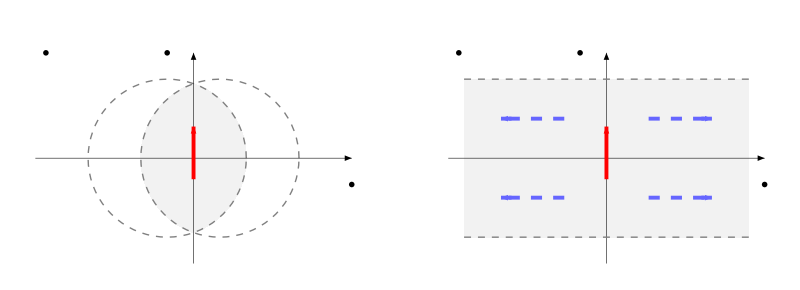

```mathematica
tp=GraphicsRow[{b,a}]
```

```mathematica
Export[path<>"transverse.pdf",tp,"PDF"];
```

```mathematica
lines1=Graphics[{Red,Thickness[0.007],Arrowheads[0.05],
Arrow[{{-0.4,0},{0.6 ,0 }}]
}];

lines2=Graphics[{Black,Thickness[0.001],
Arrow[{{-3,0},{3 ,0 }}],
Arrow[{{0,-2},{0,2}}]
}];

lines3=Graphics[{Dashed,Gray,
Line[{{-2.7,1.5},{2.7 ,1.5 }}],
Line[{{-2.7,-1.5},{2.7 ,-1.5 }}]
}];

lines4a=Graphics[{Lighter[Blue,0.4],Dashing[0.02],Thickness[0.007],
Line[{{0.8,0.75},{1.9 ,0.75 }}],
Line[{{0.8,-0.75},{1.9 ,-0.75 }}],
Line[{{-0.8,0.75},{-1.9 ,0.75 }}],
Line[{{-0.8,-0.75},{-1.9 ,-0.75 }}]
}];
lines4b=Graphics[{Lighter[Blue,0.4],Thickness[0.007],Arrowheads[0.05],
Arrow[{{1.8,0.75},{2 ,0.75 }}],
Arrow[{{1.8,-0.75},{2 ,-0.75 }}],
Arrow[{{-1.8,0.75},{-2 ,0.75 }}],
Arrow[{{-1.8,-0.75},{-2 ,-0.75 }}]
}];

des=Graphics[{Black,Thin, 
Text[Style[MaTeX["\\bm{z} ","Preamble"->{"\\usepackage{bm}"},Magnification->1.6]],{3,-0.5}],
Text[Style[MaTeX["\\bm{y} ","Preamble"->{"\\usepackage{bm}"},Magnification->1.6]],{-0.5,2}]
}];

p=Show[{lines2,lines1,lines3,lines4a,lines4b,des},BaseStyle->{
FontFamily->"Arial",
FontSize->14,
FontWeight->"Bold",Boxed->False
}];

c=Show[RegionPlot[Abs[y]<1.5&& Abs[x]<2.7,{x,-3,3},{y,-2,2.5},Frame-> False,Axes-> False,AxesStyle->Directive[Thickness[0.005],Gray],AspectRatio->4.5/6,PlotStyle->Directive[Lighter[Gray,0.9]],BoundaryStyle->None],p]
```

```mathematica
cl=Show[RegionPlot[Abs[x]>5,{x,-3,0},{y,-2,2.5},Frame-> False,Axes-> False,AspectRatio->4.5/3,PlotStyle->Directive[Lighter[Gray,0.9]],BoundaryStyle->None]]
```

-Graphics-

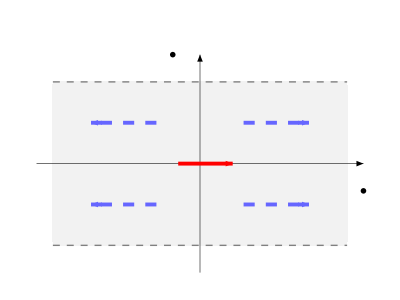

```mathematica
lp=GraphicsRow[{cl,c,cl}]
```

```mathematica
Export[path<>"longitudinal.pdf",lp,"PDF"];
```

```mathematica
Sc[a_,b_,c_]:=S[a,b,c]+S[b,c,a]+S[c,a,b]
```

```mathematica
S[a_,b_,c_]:=u[a](x[b]u[c]-x[c]u[b])
```

```mathematica
Sc[i,j,k]//Simplify
```

0